```mathematica
data1 = Import["/net/home/f09/bajennissen/research/DAY201/tau_day_data/368nm.dat"]
data1hour=Drop[data1, None,1]
data2 = Import["/net/home/f09/bajennissen/research/DAY201/tau_day_data/412nm.dat"]
data2hour=Drop[data2,None,1]
data3 = Import["/net/home/f09/bajennissen/research/DAY201/tau_day_data/500nm.dat"]
data3hour=Drop[data3,None,1]
data4 = Import["/net/home/f09/bajennissen/research/DAY201/tau_day_data/610nm.dat"]
data4hour=Drop[data4,None,1]
data5 = Import["/net/home/f09/bajennissen/research/DAY201/tau_day_data/675nm.dat"]
data5hour=Drop[data5,None,1]
data6= Import["/net/home/f09/bajennissen/research/DAY201/tau_day_data/778nm.dat"]
data6hour=Drop[data6,None,1]
data7 = Import["/net/home/f09/bajennissen/research/DAY201/tau_day_data/862nm.dat"]
data7hour=Drop[data7,None,1]
```

{{201.347,8.33333,0.158426},{201.357,8.56667,0.162219},{201.365,8.76667,0.165577},{201.372,8.93333,0.204669},{201.381,9.15,0.198535},{201.387,9.3,0.184271},{201.399,9.58333,0.190876},{201.408,9.78333,0.196929},{201.415,9.95,0.216614},{201.423,10.15,0.215272},{201.429,10.3,0.204103},{201.438,10.5,0.244228},{201.447,10.7167,0.278339},{201.459,11.0167,0.430778},{201.532,12.7667,0.46788},{201.547,13.1333,0.348491},{201.606,14.55,0.23992},{201.617,14.8,0.293515}}

{{8.33333,0.158426},{8.56667,0.162219},{8.76667,0.165577},{8.93333,0.204669},{9.15,0.198535},{9.3,0.184271},{9.58333,0.190876},{9.78333,0.196929},{9.95,0.216614},{10.15,0.215272},{10.3,0.204103},{10.5,0.244228},{10.7167,0.278339},{11.0167,0.430778},{12.7667,0.46788},{13.1333,0.348491},{14.55,0.23992},{14.8,0.293515}}

{{201.347,8.33333,0.166533},{201.357,8.56667,0.17023},{201.365,8.76667,0.180454},{201.372,8.93333,0.204519},{201.381,9.15,0.207436},{201.387,9.3,0.190381},{201.399,9.58333,0.19549},{201.408,9.78333,0.214873},{201.415,9.95,0.22559},{201.423,10.15,0.230961},{201.429,10.3,0.221641},{201.438,10.5,0.250554},{201.447,10.7167,0.27931},{201.459,11.0167,0.354069},{201.514,12.3333,2.10588},{201.532,12.7667,0.379318},{201.547,13.1333,0.291115},{201.606,14.55,0.261296},{201.617,14.8,0.295202}}

{{8.33333,0.166533},{8.56667,0.17023},{8.76667,0.180454},{8.93333,0.204519},{9.15,0.207436},{9.3,0.190381},{9.58333,0.19549},{9.78333,0.214873},{9.95,0.22559},{10.15,0.230961},{10.3,0.221641},{10.5,0.250554},{10.7167,0.27931},{11.0167,0.354069},{12.3333,2.10588},{12.7667,0.379318},{13.1333,0.291115},{14.55,0.261296},{14.8,0.295202}}

{{201.347,8.33333,0.129118},{201.357,8.56667,0.128436},{201.365,8.76667,0.136184},{201.372,8.93333,0.15813},{201.381,9.15,0.162026},{201.387,9.3,0.149793},{201.399,9.58333,0.155135},{201.408,9.78333,0.16696},{201.415,9.95,0.176253},{201.423,10.15,0.177441},{201.429,10.3,0.177262},{201.438,10.5,0.190675},{201.447,10.7167,0.201729},{201.459,11.0167,0.237108},{201.514,12.3333,1.34548},{201.532,12.7667,0.240833},{201.547,13.1333,0.161493},{201.606,14.55,0.18387},{201.617,14.8,0.210805}}

{{8.33333,0.129118},{8.56667,0.128436},{8.76667,0.136184},{8.93333,0.15813},{9.15,0.162026},{9.3,0.149793},{9.58333,0.155135},{9.78333,0.16696},{9.95,0.176253},{10.15,0.177441},{10.3,0.177262},{10.5,0.190675},{10.7167,0.201729},{11.0167,0.237108},{12.3333,1.34548},{12.7667,0.240833},{13.1333,0.161493},{14.55,0.18387},{14.8,0.210805}}

{{201.347,8.33333,0.134028},{201.357,8.56667,0.132173},{201.365,8.76667,0.13846},{201.372,8.93333,0.151315},{201.381,9.15,0.155824},{201.387,9.3,0.147961},{201.399,9.58333,0.153828},{201.408,9.78333,0.159781},{201.415,9.95,0.167601},{201.423,10.15,0.168749},{201.429,10.3,0.165071},{201.438,10.5,0.177256},{201.447,10.7167,0.188652},{201.459,11.0167,0.226317},{201.514,12.3333,1.46969},{201.532,12.7667,0.22584},{201.547,13.1333,0.138566},{201.606,14.55,0.151292},{201.617,14.8,0.177992}}

{{8.33333,0.134028},{8.56667,0.132173},{8.76667,0.13846},{8.93333,0.151315},{9.15,0.155824},{9.3,0.147961},{9.58333,0.153828},{9.78333,0.159781},{9.95,0.167601},{10.15,0.168749},{10.3,0.165071},{10.5,0.177256},{10.7167,0.188652},{11.0167,0.226317},{12.3333,1.46969},{12.7667,0.22584},{13.1333,0.138566},{14.55,0.151292},{14.8,0.177992}}

{{201.347,8.33333,0.110254},{201.357,8.56667,0.103358},{201.365,8.76667,0.109557},{201.372,8.93333,0.123904},{201.381,9.15,0.124408},{201.387,9.3,0.11782},{201.399,9.58333,0.126057},{201.408,9.78333,0.131949},{201.415,9.95,0.140194},{201.423,10.15,0.142408},{201.429,10.3,0.137949},{201.438,10.5,0.148449},{201.447,10.7167,0.168138},{201.459,11.0167,0.22553},{201.514,12.3333,1.77157},{201.532,12.7667,0.233041},{201.547,13.1333,0.129173},{201.606,14.55,0.123409},{201.617,14.8,0.152865}}

{{8.33333,0.110254},{8.56667,0.103358},{8.76667,0.109557},{8.93333,0.123904},{9.15,0.124408},{9.3,0.11782},{9.58333,0.126057},{9.78333,0.131949},{9.95,0.140194},{10.15,0.142408},{10.3,0.137949},{10.5,0.148449},{10.7167,0.168138},{11.0167,0.22553},{12.3333,1.77157},{12.7667,0.233041},{13.1333,0.129173},{14.55,0.123409},{14.8,0.152865}}

{{201.347,8.33333,0.108075},{201.357,8.56667,0.111965},{201.365,8.76667,0.119177},{201.372,8.93333,0.124147},{201.381,9.15,0.122133},{201.387,9.3,0.122026},{201.399,9.58333,0.121308},{201.408,9.78333,0.134564},{201.415,9.95,0.136051},{201.423,10.15,0.145493},{201.429,10.3,0.147222},{201.438,10.5,0.163851},{201.447,10.7167,0.211019},{201.459,11.0167,0.331327},{201.514,12.3333,5.83892},{201.532,12.7667,0.327581},{201.547,13.1333,0.208659},{201.606,14.55,0.133259},{201.617,14.8,0.161243}}

{{8.33333,0.108075},{8.56667,0.111965},{8.76667,0.119177},{8.93333,0.124147},{9.15,0.122133},{9.3,0.122026},{9.58333,0.121308},{9.78333,0.134564},{9.95,0.136051},{10.15,0.145493},{10.3,0.147222},{10.5,0.163851},{10.7167,0.211019},{11.0167,0.331327},{12.3333,5.83892},{12.7667,0.327581},{13.1333,0.208659},{14.55,0.133259},{14.8,0.161243}}

{{201.347,8.33333,0.0961426},{201.357,8.56667,0.101874},{201.365,8.76667,0.101524},{201.372,8.93333,0.108766},{201.381,9.15,0.106872},{201.387,9.3,0.0996536},{201.399,9.58333,0.106337},{201.408,9.78333,0.109156},{201.415,9.95,0.124993},{201.423,10.15,0.128232},{201.429,10.3,0.125261},{201.438,10.5,0.149783},{201.447,10.7167,0.240548},{201.459,11.0167,0.491532},{201.532,12.7667,0.530319},{201.547,13.1333,0.321569},{201.606,14.55,0.133915},{201.617,14.8,0.158153}}

{{8.33333,0.0961426},{8.56667,0.101874},{8.76667,0.101524},{8.93333,0.108766},{9.15,0.106872},{9.3,0.0996536},{9.58333,0.106337},{9.78333,0.109156},{9.95,0.124993},{10.15,0.128232},{10.3,0.125261},{10.5,0.149783},{10.7167,0.240548},{11.0167,0.491532},{12.7667,0.530319},{13.1333,0.321569},{14.55,0.133915},{14.8,0.158153}}

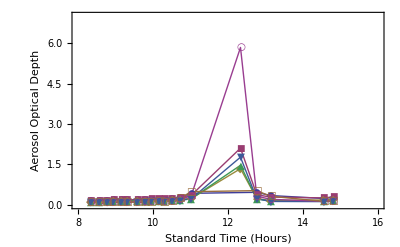

```mathematica
<<PlotLegends`
DataPlot=ListPlot[{data1hour,data2hour,data3hour,data4hour,data5hour,data6hour,data7hour}, PlotStyle->PointSize[0.02],PlotMarkers->Automatic,Joined->True,PlotLegend->{"368nm","412nm","500nm","610nm","675nm","778nm","862nm"},LegendPosition->{1.1,-0.4}, LegendSize->{0.5,0.75},PlotRange->{{8,16},{0,7}},Frame->True, AxesOrigin-> {8,0},LegendShadow->None,FrameLabel->{{"Aerosol Optical Depth",""},{"Standard Time (Hours)","Day 201 July 20th, 2010"}}]
```